```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

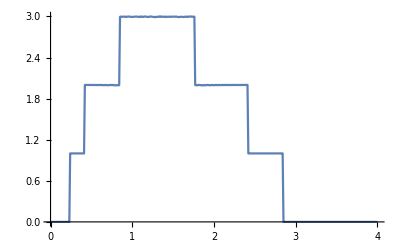

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],(*RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13}],*)Table[imp,36]]]
```

{imp,imp,imp8,imp2,imp,imp,imp,imp13,imp12,imp,imp7,imp,imp,imp,imp,imp10,imp,imp6,imp5,imp,imp,imp,imp11,imp,imp,imp,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp,imp14,imp,imp,imp,imp,imp,imp,imp,imp3,imp4,imp,imp,imp1}

```mathematica
m2[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp5,imp1,imp8,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp6,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp14,imp9,imp11,imp,imp,imp,imp,imp2,imp3,imp,imp,imp,imp,imp,imp,imp,imp7,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,50}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
f[M_]:=Table[{ω,Mean[Table[m2[ω,0.5],M]]},{ω,Range[0,1.5,0.01]}]
```

```mathematica
f[50]
```

{{0.,2.74091×10^-7},{0.01,2.58047×10^-7},{0.02,2.58556×10^-7},{0.03,2.60663×10^-7},{0.04,2.69039×10^-7},{0.05,2.69661×10^-7},{0.06,2.81656×10^-7},{0.07,3.13122×10^-7},{0.08,3.07871×10^-7},{0.09,3.41942×10^-7},{0.1,3.57777×10^-7},{0.11,3.6631×10^-7},{0.12,4.22709×10^-7},{0.13,4.88488×10^-7},{0.14,5.44656×10^-7},{0.15,5.98248×10^-7},{0.16,7.60744×10^-7},{0.17,9.52189×10^-7},{0.18,1.18991×10^-6},{0.19,1.64692×10^-6},{0.2,2.59747×10^-6},{0.21,4.70387×10^-6},{0.22,0.0000111172},{0.23,0.0000965318},{0.24,0.13169},{0.25,0.479042},{0.26,0.626291},{0.27,0.696792},{0.28,0.684582},{0.29,0.772777},{0.3,0.811266},{0.31,0.791676},{0.32,0.834334},{0.33,0.849437},{0.34,0.837838},{0.35,0.87012},{0.36,0.839311},{0.37,0.848041},{0.38,0.866109},{0.39,0.82259},{0.4,0.828727},{0.41,0.730788},{0.42,0.843647},{0.43,0.853477},{0.44,0.840757},{0.45,0.976935},{0.46,1.20347},{0.47,1.23701},{0.48,1.38706},{0.49,1.41467},{0.5,1.45441},{0.51,1.44694},{0.52,1.48366},{0.53,1.46197},{0.54,1.49356},{0.55,1.53261},{0.56,1.49481},{0.57,1.56147},{0.58,1.58999},{0.59,1.59617},{0.6,1.53995},{0.61,1.62686},{0.62,1.64881},{0.63,1.6405},{0.64,1.6555},{0.65,1.64048},{0.66,1.63236},{0.67,1.65713},{0.68,1.68555},{0.69,1.6856},{0.7,1.69396},{0.71,1.67186},{0.72,1.68226},{0.73,1.69069},{0.74,1.69254},{0.75,1.69441},{0.76,1.67484},{0.77,1.70863},{0.78,1.72003},{0.79,1.71038},{0.8,1.68936},{0.81,1.72665},{0.82,1.7316},{0.83,1.69262},{0.84,1.62008},{0.85,1.05413},{0.86,1.11895},{0.87,1.184},{0.88,1.39523},{0.89,1.71781},{0.9,1.81877},{0.91,1.90581},{0.92,1.95285},{0.93,2.05925},{0.94,2.08804},{0.95,2.1665},{0.96,2.2646},{0.97,2.34771},{0.98,2.37351},{0.99,2.35568},{1.,2.41164},{1.01,2.39721},{1.02,2.35625},{1.03,2.17812},{1.04,1.70401},{1.05,0.996757},{1.06,0.322875},{1.07,0.39192},{1.08,0.611072},{1.09,0.94992},{1.1,1.34195},{1.11,1.36842},{1.12,1.51721},{1.13,1.58613},{1.14,1.71296},{1.15,1.64649},{1.16,1.79197},{1.17,1.74352},{1.18,1.82898},{1.19,1.85942},{1.2,1.89346},{1.21,1.90155},{1.22,1.92622},{1.23,1.977},{1.24,1.88924},{1.25,2.00708},{1.26,2.01812},{1.27,1.85026},{1.28,1.99362},{1.29,1.97431},{1.3,2.06201},{1.31,1.99541},{1.32,1.9511},{1.33,2.0106},{1.34,1.9855},{1.35,2.08356},{1.36,2.0006},{1.37,1.97095},{1.38,1.99759},{1.39,1.97757},{1.4,2.02819},{1.41,1.98564},{1.42,2.02518},{1.43,1.97169},{1.44,1.89343},{1.45,1.95959},{1.46,1.93929},{1.47,1.90985},{1.48,1.87203},{1.49,1.91349},{1.5,1.89363}}

```mathematica
f[100]
```

{{0.,2.71594×10^-7},{0.01,2.54977×10^-7},{0.02,2.55652×10^-7},{0.03,2.53658×10^-7},{0.04,2.6277×10^-7},{0.05,2.89935×10^-7},{0.06,2.94501×10^-7},{0.07,3.0309×10^-7},{0.08,3.14857×10^-7},{0.09,3.37436×10^-7},{0.1,3.70946×10^-7},{0.11,3.83754×10^-7},{0.12,4.45218×10^-7},{0.13,4.80877×10^-7},{0.14,5.55865×10^-7},{0.15,6.16375×10^-7},{0.16,7.59193×10^-7},{0.17,9.05866×10^-7},{0.18,1.19001×10^-6},{0.19,1.66227×10^-6},{0.2,2.62611×10^-6},{0.21,4.4781×10^-6},{0.22,0.0000115932},{0.23,0.0000979822},{0.24,0.106545},{0.25,0.366088},{0.26,0.57957},{0.27,0.696812},{0.28,0.735681},{0.29,0.781857},{0.3,0.778275},{0.31,0.812788},{0.32,0.842788},{0.33,0.818116},{0.34,0.824214},{0.35,0.846397},{0.36,0.847966},{0.37,0.861129},{0.38,0.839384},{0.39,0.836632},{0.4,0.819222},{0.41,0.758211},{0.42,0.756712},{0.43,0.768899},{0.44,0.935395},{0.45,1.08736},{0.46,1.16477},{0.47,1.26314},{0.48,1.32669},{0.49,1.32044},{0.5,1.39398},{0.51,1.4531},{0.52,1.47808},{0.53,1.50835},{0.54,1.53037},{0.55,1.59361},{0.56,1.56891},{0.57,1.58972},{0.58,1.61736},{0.59,1.5429},{0.6,1.61239},{0.61,1.61271},{0.62,1.64691},{0.63,1.59899},{0.64,1.64735},{0.65,1.68156},{0.66,1.64939},{0.67,1.63303},{0.68,1.66708},{0.69,1.66983},{0.7,1.62814},{0.71,1.68236},{0.72,1.64274},{0.73,1.6865},{0.74,1.68073},{0.75,1.71025},{0.76,1.69128},{0.77,1.69042},{0.78,1.68507},{0.79,1.69961},{0.8,1.72694},{0.81,1.68242},{0.82,1.72292},{0.83,1.69044},{0.84,1.66416},{0.85,1.0224},{0.86,1.07456},{0.87,1.20113},{0.88,1.41973},{0.89,1.67615},{0.9,1.78922},{0.91,1.879},{0.92,1.9676},{0.93,2.04784},{0.94,2.13286},{0.95,2.19653},{0.96,2.23817},{0.97,2.21309},{0.98,2.30256},{0.99,2.31772},{1.,2.38981},{1.01,2.41335},{1.02,2.35599},{1.03,2.1853},{1.04,1.71441},{1.05,0.915851},{1.06,0.36504},{1.07,0.343893},{1.08,0.638265},{1.09,0.882182},{1.1,1.23698},{1.11,1.37536},{1.12,1.45995},{1.13,1.50268},{1.14,1.68578},{1.15,1.64896},{1.16,1.842},{1.17,1.80442},{1.18,1.86891},{1.19,1.91538},{1.2,1.86404},{1.21,1.92243},{1.22,1.94417},{1.23,1.89402},{1.24,1.94536},{1.25,1.95228},{1.26,2.01094},{1.27,1.98463},{1.28,1.9619},{1.29,1.98138},{1.3,1.95425},{1.31,1.98927},{1.32,2.00343},{1.33,2.00355},{1.34,1.97985},{1.35,2.00689},{1.36,1.99413},{1.37,2.02296},{1.38,2.00252},{1.39,1.97608},{1.4,2.00996},{1.41,1.98903},{1.42,1.91164},{1.43,1.97198},{1.44,1.9729},{1.45,1.929},{1.46,1.92467},{1.47,1.92161},{1.48,1.92329},{1.49,1.91344},{1.5,1.93897}}

```mathematica
f[200]
```

{{0.,2.70506×10^-7},{0.01,2.48597×10^-7},{0.02,2.57357×10^-7},{0.03,2.61853×10^-7},{0.04,2.65714×10^-7},{0.05,2.85592×10^-7},{0.06,2.89269×10^-7},{0.07,3.06707×10^-7},{0.08,3.207×10^-7},{0.09,3.44625×10^-7},{0.1,3.5749×10^-7},{0.11,3.76989×10^-7},{0.12,4.15646×10^-7},{0.13,4.75801×10^-7},{0.14,5.33209×10^-7},{0.15,6.32002×10^-7},{0.16,7.51185×10^-7},{0.17,9.36734×10^-7},{0.18,1.21644×10^-6},{0.19,1.68074×10^-6},{0.2,2.5096×10^-6},{0.21,4.6037×10^-6},{0.22,0.0000120202},{0.23,0.0000983895},{0.24,0.131246},{0.25,0.385383},{0.26,0.569841},{0.27,0.658131},{0.28,0.69474},{0.29,0.756022},{0.3,0.781826},{0.31,0.821072},{0.32,0.816164},{0.33,0.819564},{0.34,0.819409},{0.35,0.82729},{0.36,0.842103},{0.37,0.85102},{0.38,0.844725},{0.39,0.843041},{0.4,0.833598},{0.41,0.710011},{0.42,0.718967},{0.43,0.746268},{0.44,0.892367},{0.45,1.02478},{0.46,1.15336},{0.47,1.26191},{0.48,1.32503},{0.49,1.33077},{0.5,1.39827},{0.51,1.45841},{0.52,1.47641},{0.53,1.49752},{0.54,1.50873},{0.55,1.55051},{0.56,1.57076},{0.57,1.57104},{0.58,1.60342},{0.59,1.59249},{0.6,1.60506},{0.61,1.62862},{0.62,1.6097},{0.63,1.6204},{0.64,1.64467},{0.65,1.6478},{0.66,1.64116},{0.67,1.64448},{0.68,1.6725},{0.69,1.66189},{0.7,1.64867},{0.71,1.6755},{0.72,1.66587},{0.73,1.68477},{0.74,1.68737},{0.75,1.70368},{0.76,1.70605},{0.77,1.68467},{0.78,1.71111},{0.79,1.70451},{0.8,1.70446},{0.81,1.71024},{0.82,1.71193},{0.83,1.71604},{0.84,1.64205},{0.85,0.997683},{0.86,1.03122},{0.87,1.22637},{0.88,1.45181},{0.89,1.61173},{0.9,1.7994},{0.91,1.90585},{0.92,1.99849},{0.93,2.03786},{0.94,2.15352},{0.95,2.16473},{0.96,2.28364},{0.97,2.25562},{0.98,2.31185},{0.99,2.31927},{1.,2.37199},{1.01,2.40807},{1.02,2.32962},{1.03,2.15666},{1.04,1.69004},{1.05,0.840459},{1.06,0.362475},{1.07,0.392682},{1.08,0.616639},{1.09,0.907272},{1.1,1.21159},{1.11,1.41443},{1.12,1.44962},{1.13,1.5415},{1.14,1.68839},{1.15,1.697},{1.16,1.78558},{1.17,1.81263},{1.18,1.83317},{1.19,1.89749},{1.2,1.89775},{1.21,1.89447},{1.22,1.92758},{1.23,1.9669},{1.24,1.94142},{1.25,1.96612},{1.26,1.96317},{1.27,1.9553},{1.28,1.99176},{1.29,1.98785},{1.3,2.00604},{1.31,1.98442},{1.32,1.9584},{1.33,1.98663},{1.34,1.96121},{1.35,2.00115},{1.36,2.00501},{1.37,2.0192},{1.38,2.00129},{1.39,1.95535},{1.4,1.96423},{1.41,1.97773},{1.42,1.97206},{1.43,1.92439},{1.44,1.94142},{1.45,1.942},{1.46,1.91692},{1.47,1.90755},{1.48,1.93223},{1.49,1.93108},{1.5,1.94158}}

```mathematica
f[400]
```

{{0.,2.71102×10^-7},{0.01,2.46782×10^-7},{0.02,2.54833×10^-7},{0.03,2.63165×10^-7},{0.04,2.67826×10^-7},{0.05,2.75251×10^-7},{0.06,2.93978×10^-7},{0.07,3.0433×10^-7},{0.08,3.20996×10^-7},{0.09,3.36599×10^-7},{0.1,3.61738×10^-7},{0.11,3.97896×10^-7},{0.12,4.31035×10^-7},{0.13,4.7424×10^-7},{0.14,5.43718×10^-7},{0.15,6.36029×10^-7},{0.16,7.5395×10^-7},{0.17,9.23499×10^-7},{0.18,1.19837×10^-6},{0.19,1.64452×10^-6},{0.2,2.49141×10^-6},{0.21,4.63967×10^-6},{0.22,0.0000117662},{0.23,0.0000964704},{0.24,0.101701},{0.25,0.423143},{0.26,0.566071},{0.27,0.673141},{0.28,0.723397},{0.29,0.752332},{0.3,0.773845},{0.31,0.803452},{0.32,0.826928},{0.33,0.831761},{0.34,0.821302},{0.35,0.835695},{0.36,0.849565},{0.37,0.855794},{0.38,0.854201},{0.39,0.838505},{0.4,0.812575},{0.41,0.727618},{0.42,0.670524},{0.43,0.768502},{0.44,0.86597},{0.45,1.00997},{0.46,1.16873},{0.47,1.2339},{0.48,1.31927},{0.49,1.3602},{0.5,1.38407},{0.51,1.43748},{0.52,1.46455},{0.53,1.50938},{0.54,1.52017},{0.55,1.52746},{0.56,1.56435},{0.57,1.58936},{0.58,1.60675},{0.59,1.59598},{0.6,1.5984},{0.61,1.6258},{0.62,1.61975},{0.63,1.63377},{0.64,1.65668},{0.65,1.63989},{0.66,1.64932},{0.67,1.65848},{0.68,1.65818},{0.69,1.66531},{0.7,1.67506},{0.71,1.68336},{0.72,1.67595},{0.73,1.68923},{0.74,1.69209},{0.75,1.68017},{0.76,1.69486},{0.77,1.68041},{0.78,1.70598},{0.79,1.70763},{0.8,1.71582},{0.81,1.70324},{0.82,1.70144},{0.83,1.69075},{0.84,1.64606},{0.85,1.0008},{0.86,1.01824},{0.87,1.0936},{0.88,1.4705},{0.89,1.66817},{0.9,1.8139},{0.91,1.8782},{0.92,2.02662},{0.93,2.07964},{0.94,2.14454},{0.95,2.17122},{0.96,2.25092},{0.97,2.27553},{0.98,2.35101},{0.99,2.34384},{1.,2.40865},{1.01,2.38269},{1.02,2.33169},{1.03,2.16121},{1.04,1.76864},{1.05,0.916887},{1.06,0.372889},{1.07,0.413934},{1.08,0.628528},{1.09,0.911954},{1.1,1.20452},{1.11,1.36845},{1.12,1.47264},{1.13,1.56698},{1.14,1.67538},{1.15,1.70146},{1.16,1.78286},{1.17,1.81784},{1.18,1.8524},{1.19,1.87279},{1.2,1.89045},{1.21,1.92025},{1.22,1.93725},{1.23,1.95608},{1.24,1.93752},{1.25,1.93076},{1.26,1.99146},{1.27,1.97438},{1.28,1.9694},{1.29,1.98147},{1.3,1.98392},{1.31,1.99126},{1.32,1.99132},{1.33,1.98039},{1.34,1.95441},{1.35,1.99877},{1.36,2.00023},{1.37,2.00533},{1.38,2.02408},{1.39,1.95643},{1.4,1.97043},{1.41,1.9745},{1.42,1.95158},{1.43,1.97159},{1.44,1.9477},{1.45,1.92326},{1.46,1.90504},{1.47,1.92996},{1.48,1.92532},{1.49,1.94075},{1.5,1.91229}}

```mathematica
f[800]
```

{{0.,2.6951×10^-7},{0.01,2.51648×10^-7},{0.02,2.59872×10^-7},{0.03,2.63997×10^-7},{0.04,2.67399×10^-7},{0.05,2.7968×10^-7},{0.06,2.90874×10^-7},{0.07,2.97387×10^-7},{0.08,3.19714×10^-7},{0.09,3.36456×10^-7},{0.1,3.54112×10^-7},{0.11,3.85798×10^-7},{0.12,4.27383×10^-7},{0.13,4.76213×10^-7},{0.14,5.40452×10^-7},{0.15,6.29449×10^-7},{0.16,7.55897×10^-7},{0.17,9.29433×10^-7},{0.18,1.18053×10^-6},{0.19,1.65914×10^-6},{0.2,2.53311×10^-6},{0.21,4.59419×10^-6},{0.22,0.0000117049},{0.23,0.000100937},{0.24,0.0924662},{0.25,0.404471},{0.26,0.575763},{0.27,0.68237},{0.28,0.735182},{0.29,0.757292},{0.3,0.786365},{0.31,0.810489},{0.32,0.810241},{0.33,0.825592},{0.34,0.844083},{0.35,0.833667},{0.36,0.838096},{0.37,0.842089},{0.38,0.846886},{0.39,0.844211},{0.4,0.815284},{0.41,0.726562},{0.42,0.705215},{0.43,0.754207},{0.44,0.857259},{0.45,1.03786},{0.46,1.14535},{0.47,1.24046},{0.48,1.32747},{0.49,1.37621},{0.5,1.42815},{0.51,1.4632},{0.52,1.48307},{0.53,1.48634},{0.54,1.52304},{0.55,1.55498},{0.56,1.55677},{0.57,1.56607},{0.58,1.59496},{0.59,1.58983},{0.6,1.61395},{0.61,1.62693},{0.62,1.63833},{0.63,1.62391},{0.64,1.64603},{0.65,1.65356},{0.66,1.65575},{0.67,1.65223},{0.68,1.66171},{0.69,1.66345},{0.7,1.6622},{0.71,1.67},{0.72,1.68887},{0.73,1.68201},{0.74,1.69413},{0.75,1.69517},{0.76,1.69577},{0.77,1.69234},{0.78,1.69688},{0.79,1.70029},{0.8,1.71503},{0.81,1.70949},{0.82,1.7057},{0.83,1.69698},{0.84,1.66183},{0.85,0.981643},{0.86,1.0049},{0.87,1.17811},{0.88,1.45845},{0.89,1.6648},{0.9,1.7965},{0.91,1.94458},{0.92,2.00029},{0.93,2.06683},{0.94,2.14349},{0.95,2.18357},{0.96,2.22159},{0.97,2.28625},{0.98,2.32718},{0.99,2.34221},{1.,2.37078},{1.01,2.41392},{1.02,2.35076},{1.03,2.19016},{1.04,1.70759},{1.05,0.917033},{1.06,0.38591},{1.07,0.379877},{1.08,0.589665},{1.09,0.943063},{1.1,1.2068},{1.11,1.35263},{1.12,1.47162},{1.13,1.57062},{1.14,1.66591},{1.15,1.69893},{1.16,1.79796},{1.17,1.80972},{1.18,1.85386},{1.19,1.86858},{1.2,1.8828},{1.21,1.9188},{1.22,1.93092},{1.23,1.9519},{1.24,1.92656},{1.25,1.96803},{1.26,1.97035},{1.27,1.96495},{1.28,1.97921},{1.29,1.95483},{1.3,1.99067},{1.31,1.98141},{1.32,2.00409},{1.33,2.00631},{1.34,1.98067},{1.35,2.00111},{1.36,1.98898},{1.37,2.00654},{1.38,1.99719},{1.39,1.97999},{1.4,1.97825},{1.41,1.98032},{1.42,1.9687},{1.43,1.96083},{1.44,1.95271},{1.45,1.94202},{1.46,1.91349},{1.47,1.92714},{1.48,1.92537},{1.49,1.91882},{1.5,1.92066}}

```mathematica
f[1600]
```

{{0.,2.69885×10^-7},{0.01,2.51221×10^-7},{0.02,2.54978×10^-7},{0.03,2.64417×10^-7},{0.04,2.71233×10^-7},{0.05,2.79251×10^-7},{0.06,2.91009×10^-7},{0.07,3.03123×10^-7},{0.08,3.18429×10^-7},{0.09,3.36784×10^-7},{0.1,3.56894×10^-7},{0.11,3.87839×10^-7},{0.12,4.255×10^-7},{0.13,4.74498×10^-7},{0.14,5.38156×10^-7},{0.15,6.34334×10^-7},{0.16,7.52446×10^-7},{0.17,9.28694×10^-7},{0.18,1.19677×10^-6},{0.19,1.65168×10^-6},{0.2,2.51674×10^-6},{0.21,4.55276×10^-6},{0.22,0.0000117361},{0.23,0.000102344},{0.24,0.104834},{0.25,0.402589},{0.26,0.578882},{0.27,0.683837},{0.28,0.730945},{0.29,0.761375},{0.3,0.787602},{0.31,0.803895},{0.32,0.814057},{0.33,0.824537},{0.34,0.834834},{0.35,0.835552},{0.36,0.840028},{0.37,0.847006},{0.38,0.845266},{0.39,0.842367},{0.4,0.822121},{0.41,0.729371},{0.42,0.68691},{0.43,0.755205},{0.44,0.881582},{0.45,1.04967},{0.46,1.13926},{0.47,1.25819},{0.48,1.3207},{0.49,1.36844},{0.5,1.42398},{0.51,1.47442},{0.52,1.47793},{0.53,1.50487},{0.54,1.52309},{0.55,1.55135},{0.56,1.55619},{0.57,1.56706},{0.58,1.58339},{0.59,1.5869},{0.6,1.6146},{0.61,1.61881},{0.62,1.62558},{0.63,1.62907},{0.64,1.63784},{0.65,1.63804},{0.66,1.65341},{0.67,1.6623},{0.68,1.66125},{0.69,1.66768},{0.7,1.66012},{0.71,1.67726},{0.72,1.67474},{0.73,1.68822},{0.74,1.6917},{0.75,1.6938},{0.76,1.69907},{0.77,1.70403},{0.78,1.7121},{0.79,1.70998},{0.8,1.71936},{0.81,1.71762},{0.82,1.70902},{0.83,1.70905},{0.84,1.65844},{0.85,0.988128},{0.86,0.963815},{0.87,1.19023},{0.88,1.46931},{0.89,1.64999},{0.9,1.75321},{0.91,1.91395},{0.92,1.99675},{0.93,2.08593},{0.94,2.13186},{0.95,2.19128},{0.96,2.23915},{0.97,2.2825},{0.98,2.33848},{0.99,2.34656},{1.,2.3815},{1.01,2.40568},{1.02,2.34242},{1.03,2.17238},{1.04,1.72211},{1.05,0.90385},{1.06,0.38036},{1.07,0.374048},{1.08,0.612802},{1.09,0.92709},{1.1,1.18023},{1.11,1.36327},{1.12,1.4767},{1.13,1.571},{1.14,1.65142},{1.15,1.71886},{1.16,1.79629},{1.17,1.81332},{1.18,1.85719},{1.19,1.86463},{1.2,1.90848},{1.21,1.91587},{1.22,1.95739},{1.23,1.94833},{1.24,1.93087},{1.25,1.96263},{1.26,1.97793},{1.27,1.96082},{1.28,1.97612},{1.29,1.96878},{1.3,1.98996},{1.31,1.99277},{1.32,1.97986},{1.33,2.01618},{1.34,1.97603},{1.35,1.99685},{1.36,1.99411},{1.37,2.00053},{1.38,2.00684},{1.39,1.9773},{1.4,1.96942},{1.41,1.98226},{1.42,1.95232},{1.43,1.96316},{1.44,1.9631},{1.45,1.93156},{1.46,1.91117},{1.47,1.9378},{1.48,1.93714},{1.49,1.92135},{1.5,1.91169}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m50.dat",%20]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m100.dat",%22]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m200.dat",%23]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m400.dat",%24]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m800.dat",%25]
Export["/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m1600.dat",%26]
```

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m50.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m100.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m200.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m400.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m800.dat

/home/shardulmukim/PhD/fwi/7AGNR/50unitcells/errorm2/m1600.dat